```mathematica
n=3;
phenotypelist=Tuples[{0,1},n];
phenotypelist1=Reverse@Select[phenotypelist,Count[#,1]==1&];
```

```mathematica
alpha=Table[10,n];
r=Table[1,n+1];
d=Table[1*10^-6,n];
y=Table[10^-5,n];
S0=20000;
mout0=Join[{S0},Table[0,n]];
X0=Table[10^-4,n];
p=0.01;
```

```mathematica
(*cond1:0<rb<ra<1*)
ralist={0.9};
d1=d[[1]]/y[[1]];
Ig3list={1,5,10,25,50,100};
Bigset={};
Do[
rblist=Table[i,{i,(ralist[[j]]/50),ralist[[j]]-(ralist[[j]]/50),ralist[[j]]/50}];
paraset={};
Igc3list=Rationalize@Table[{Ig3list[[k]],(ralist[[j]])*(d1/ralist[[j]])/Ig3list[[k]]},{k,Length@Ig3list}];
Do[
Ig1=(d1*rblist[[i]]-ralist[[j]]*(d1/ralist[[j]])* ralist[[j]]* rblist[[i]])/(ralist[[j]]*(d1/ralist[[j]])*ralist[[j]]-d1 rblist[[i]]);
c1=-(d1*ralist[[j]]*(d1/ralist[[j]])(-1+ rblist[[i]]))/((d1-ralist[[j]]*(d1/ralist[[j]])*ralist[[j]])  rblist[[i]]);
paraset=Join[paraset,{{Ig1,c1}}];
,{i,Length@rblist}];
(*paraset=Select[paraset,#[[1]]>0&&#[[2]]>0&];*)
Parasets=Partition[Flatten[Table[{paraset[[k1]],paraset[[k2]]},{k1,1,Length@paraset},{k2,1,Length@paraset}]],4];
bigsets=Table[Join[Parasets[[j]],Igc3list[[i]]],{i,Length@Igc3list},{j,Length@Parasets}];
Bigset=Join[Bigset,bigsets];
,{j,1,1}];
Length@Bigset
```

```mathematica
asets={1,10,100};
asets=Flatten[Table[{asets[[i]],asets[[j]],asets[[k]]},{i,1,Length@asets},{j,1,Length@asets},{k,1,Length@asets}],2];
asets1=SortBy[asets,First]
Length@Parasets
```

```mathematica
Do[
list={};
list1={};
alpha=asets1[[j]];
Do[
set=First[bigsets][[i]];
Ig=Take[set,{1,-2,2}];
Ct=Take[set,{2,-1,2}];
test=Table[(Ig[[i]]*Ct[[-1]]*Ig[[-1]])/((Ig[[i]]*Ct[[i]])-Ct[[-1]]*Ig[[-1]]),{i,1,Length@Ig-1}];
mout=Table[ToExpression["mout"<>ToString@j],{j,1,n+1}];
V=Table[ToExpression["V"<>ToString@i],{i,1,n}];
min=Table[ToExpression["min"<>ToString@i<>ToString@j],{i,1,n},{j,1,n+1}];
vs=Flatten@Table[phenotypelist1[[i,j]]*alpha[[j]],{i,1,n},{j,1,1}];
vi=Table[phenotypelist1[[i,j]]*alpha[[j]]*min[[i,j]][t],{i,1,n},{j,2,n}];
vp=Table[Ig[[i]]*min[[i,n+1]][t],{i,1,n}];
v0=Table[0,{i,1,n}];
v=Transpose@Join[{v0},{vs},Transpose@vi,{vp}];
g=Table[y[[i]]*(vp[[i]]*Ct[[i]]),{i,1,n}];
var=Flatten@Join[mout,min,V];
mineqn={};
Veqn={};
Do[
mouteqn={};
Do[eqn1={min[[i,j]]'[t]==v[[i,j]]-v[[i,j+1]]+r[[j]]*(mout[[j]][t]-min[[i,j]][t])};
eqn2=If[j==1,{mout[[j]]'[t]==0},
{mout[[j]]'[t]==-Sum[V[[i]][t]*r[[j]]*(mout[[j]][t]-min[[i,j]][t]),{i,1,n}]}];
mineqn=Join[mineqn,eqn1];
mouteqn=Join[mouteqn,eqn2];
,{j,1,n+1}];
eqn3={V[[i]]'[t]==g[[i]]*V[[i]][t]*(1-Sum[V[[i]][t],{i,1,n}]/p)-d[[i]]*V[[i]][t]};
Veqn=Join[Veqn,eqn3];
,{i,1,n}];
NDeqn=Flatten@Join[mineqn,mouteqn,Veqn];
mineqn0={};
Veqn0={};
Do[
mouteqn0={};
Do[eqn01={min[[i,j]][0]==0};
eqn02={mout[[j]][0]==mout0[[j]]};
mineqn0=Join[mineqn0,eqn01];
mouteqn0=Join[mouteqn0,eqn02];
,{j,1,n+1}];
eqn30={V[[i]][0]==X0[[i]]};
Veqn0=Join[Veqn0,eqn30];
,{i,1,n}];
NDeqn0=Flatten@Join[mineqn0,mouteqn0,Veqn0];
eqn=Join[NDeqn,NDeqn0];
result=NDSolve[eqn,var,{t,0,110000000}];
moutv=First@Evaluate[Table[mout[[i]][100000000],{i,1,n+1}]/.result];
minv=Flatten@First@Evaluate[Table[min[[i,j]][100000000],{i,1,n},{j,1,n+1}]/.result];
xb=First@Evaluate[Table[V[[i]][100000000],{i,1,n}]/.result];
total=Total@xb;
xratio=Round[xb/total,0.0001];
list1=Join[list1,{Join[test,xratio,{total}]}];
list=Join[list,{Join[moutv,minv,xb,{total}]}];
If[Divisible[i,2400]==True,Print[j]];
,{i,1,Length@Parasets}];
Export[FileNameJoin[{NotebookDirectory[],"speed","Results"<>ToString[j]<>".txt"}],list];
Export[FileNameJoin[{NotebookDirectory[],"speed","PlotResults"<>ToString[j]<>".xlsx"}],list1];
,{j,1,Length@asets1}];
```

```mathematica
Parasets1
```

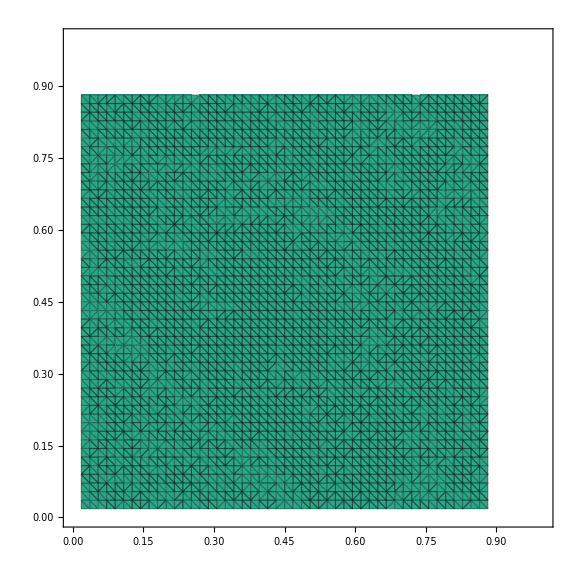

```mathematica
Gridplot1={};
Gridplot2={};
Gridplot3={};
hlist={};
numlist={};
Do[data=Flatten@Import[FileNameJoin[{NotebookDirectory[],"speed","PlotResults"<>ToString@j<>".xlsx"}]];
data=Partition[data,6];
data1=Select[data,#[[-1]]>0.0001&];
num=Length@data1;
numlist=Join[numlist,{num}];

plotdata2=Table[{data1[[i,1]],data1[[i,2]],data1[[i,-2]]*100},{i,Length@data1}];
desplot=ListDensityPlot[plotdata2,ColorFunction->"BlueGreenYellow",PlotRange->{{0,1},{0,1},{-1,100}},LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,42],ImageSize->Large,InterpolationOrder->1.0,Mesh->100];
fit=h/.FindFit[plotdata2,100*((x1^h+x2^h)/2)^(1/h),h,{x1,x2}];
theplot=Plot3D[100*((x^fit+y^fit)/2)^(1/fit),{x,0,1},{y,0,1},BoxRatios->{1, 1, 1},ImageSize->Large,PlotRange->{{0,1},{0,1},{0,105}},Boxed->True,BoxStyle->Directive[Thickness[0.005],Black,Bold,36],PlotStyle->Directive[Opacity[0.5],RGBColor[{199/255,237/255,233/255}]],LabelStyle->Directive[Black,Bold,30],AxesStyle->Directive[Thickness[0.005],Black]];
speedplot2=ListPointPlot3D[plotdata2,ImageSize->Large,BoxRatios->{1, 1, 1},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.01]],PlotRange->{{0,1},{0,1},{0,105}},Boxed->True,BoxStyle->Directive[Thickness[0.005],Black,Bold,36],LabelStyle->Directive[Black,Bold,30],AxesStyle->Directive[Thickness[0.005],Black]];
plot2=Show[theplot,speedplot2];
hlist=Join[hlist,{fit}];
Gridplot1=Join[Gridplot1,{desplot}];
Gridplot2=Join[Gridplot2,{plot2}];

plotdata4=SortBy[Table[{data1[[i,1]],data1[[i,2]],Log[10,data1[[i,3]]/(data1[[i,4]])]},{i,Length@data1}],Last];
desplot1=ListDensityPlot[plotdata4,ColorFunction->"BlueGreenYellow",PlotRange->{{0,1},{0,1},{-0.6,0.6}},LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,42],ImageSize->Large,InterpolationOrder->1.0,Mesh->All,VertexColors->Table[ColorData["BlueGreenYellow"][Rescale[plotdata4[[i,3]],{-0.6,0.6},{0,1}]],{i,1,Length@plotdata4}]];
Gridplot3=Join[Gridplot3,{desplot1}];
,{j,1,27}];
desplot1
```

```mathematica
Gridplot11=Grid[Partition[Partition[Gridplot1,9][[1]],3]];
Gridplot12=Grid[Partition[Partition[Gridplot1,9][[2]],3]];
Gridplot13=Grid[Partition[Partition[Gridplot1,9][[3]],3]];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","desplot1.tif"}],Gridplot11];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","desplot2.tif"}],Gridplot12];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","desplot3.tif"}],Gridplot13];
```

```mathematica
Gridplot21=Grid[Partition[Partition[Gridplot2,9][[1]],3]];
Gridplot22=Grid[Partition[Partition[Gridplot2,9][[2]],3]];
Gridplot23=Grid[Partition[Partition[Gridplot2,9][[3]],3]];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","3Dplot1.tif"}],Gridplot21];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","3Dplot2.tif"}],Gridplot22];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","3Dplot3.tif"}],Gridplot23];
```

```mathematica
Gridplot31=Grid[Partition[Partition[Gridplot3,9][[1]],3]];
Gridplot32=Grid[Partition[Partition[Gridplot3,9][[2]],3]];
Gridplot33=Grid[Partition[Partition[Gridplot3,9][[3]],3]];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","2Mplot1.tif"}],Gridplot31];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","2Mplot2.tif"}],Gridplot32];
Export[FileNameJoin[{NotebookDirectory[],"plot","speedplot","2Mplot3.tif"}],Gridplot33];
```

```mathematica
Ig3list1={1,5,10,25,50,100};
logIg31=Rationalize@Table[Table[Log10[Ig3list1[[i]]],{i,1,5}],6];
Ig3list2={0.25,2,0.01,100,31.6,0.0316};
logIg32=Rationalize@Table[Table[Log10[Ig3list2[[i]]],{i,1,6}],6];
```

```mathematica
hlist1=Partition[Transpose@Join[{Flatten@logIg31},{hlist[[1;;30]]}],5];
hlist2=Partition[Transpose@Join[{Flatten@logIg32},{hlist[[31;;66]]}],6];
hlist3=Transpose@Join[Transpose@hlist1,Transpose@hlist2];
hplot={};
Do[
hplot1=Show[ListLinePlot[{SortBy[N@hlist3[[i]],First]},AspectRatio->1,PlotRange->{{-2.2,2.2},{1,6}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.01],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],ListPlot[hlist3[[i]],AspectRatio->1,ImageSize->Large,PlotRange->{{-2.2,2.2},{1,6}},PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PointSize[0.03]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]];
hplot=Join[hplot,{{hplot1}}];
,{i,1,6}];
hplot1=Grid[hplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","hplot.tif"}],Gridplot11];
```

```mathematica
ClearAll[h]
predictdata=Table[{list1[[i,1]],list1[[i,2]],list1[[i,-2]]*100},{i,Length@list1}];
fit=h/.FindFit[predictdata,100*((x1^h+x2^h)/(n-1))^(1/h),h,{x1,x2}]
predictvalue=Table[100*((predictdata[[i,1]]^fit+predictdata[[i,2]]^fit)/(n-1))^(1/fit),{i,Length@predictdata}];
plotdata=Transpose@Join[{predictvalue},100*{Flatten@Take[list1,All,{-2}]}];
linearfit=LinearModelFit[plotdata,x,x,IncludeConstantBasis->False];
linearfit["AdjustedRSquared"]
linearfit["BestFitParameters"]
conf=Flatten@linearfit["ParameterConfidenceIntervals",ConfidenceLevel->.95]
plot=Show[ListPlot[plotdata,AspectRatio->1,PlotRange->{{0,100},{0,100}},ImageSize->Large,PlotStyle->Directive[RGBColor[{38/255,157/255,128/255}],PlotRange->{{-1.5,3.5},{-50,2000}},PointSize[0.0025]],Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False],Plot[linearfit[x],{x,0,100},AspectRatio->1,PlotRange->{{0,100},{0,100}},ImageSize->Large,PlotStyle->Directive[Blue,Thickness[0.01],Dashing[0.05]],PlotRange->{{-1.5,3.25},{-50,2000}},Frame->True,FrameStyle->Directive[Thickness[0.01],Black,Bold,45],Axes->False]]
Export[FileNameJoin[{NotebookDirectory[],"plot","3-member.tif"}],plot];
Length@list1
```

```mathematica
desplot1=ListDensityPlot[plotdata4,ColorFunction->"BlueGreenYellow",PlotRange->{{0,1},{0,1},{-1,1}},LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,42],ImageSize->Large,InterpolationOrder->1.0,Mesh->All,VertexColors->Table[ColorData["BlueGreenYellow"][Rescale[plotdata4[[i,3]],{-0.03,0.03},{0,1}]],{i,1,Length@plotdata4}]]
plotdata4
```